Adapted from https : // mathematica . stackexchange . com/questions/230366/solving - the - lotka - mckendrick - model - with - ndsolve

## Two Parasites (one dominant, one subordinate)

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
model[tmax_,imax_, da_,λ0d_,λ0s_, λad_, λas_,μ0u_,μ0d_,μ0s_,μad_,μas_,μadDep_,μasDep_,μadInc_,μasInc_]:=Module[
{i, t},

(* imax - number of stages (max age = imax / da) *)
(* da - ageing increment *)
(* tmax -  total time *)

(* Uninfected hosts *)
Subscript[f, u][a_]:=If[10<=a<=imax,1/10,0]; (* age-specific fertility rate *)
Subscript[μ, u][a_]:=μ0u  ; (* age-specific force of mortality *)
u0[a_]:=If[10<a<25,1,0]; (* initial age structure *)

(* Infection rate *)
Subscript[λ, d][a_]:= λ0d  + λad a;(* age-specific force of infection of dominant parasite*)
Subscript[λ, s][a_]:= λ0s + λas a; (* age-specific force of infection of subordinate parasite*)

(* Infected hosts - dominant parasite *)
Subscript[f, d][a_]:=0;(* age-specific fertility rate *)
Subscript[μ, d][a_]:=Switch[μadDep,False,μ0d,True,Switch[μadInc,True,μ0d  (1-Exp[-μad a]),False,μ0d  Exp[-μad a]]];  (* age-specific force of mortality *)
d0[a_]:=0; (* initial age structure of hosts infected by dominant parasite *)

(* Infected hosts - subordinate parasite *)
Subscript[f, s][a_]:=0;(* age-specific fertility rate *) 
Subscript[μ, s][a_]:=Switch[μasDep,False,μ0s,True,Switch[μasInc,True,μ0s  (1-Exp[-μas a]),False,μ0s  Exp[-μas a]]]; (* age-specific force of mortality *)
s0[a_]:=0; (* initial age structure of hosts infected by subordinate parasite *)

eqns=Join[
(* Change in uninfected hosts of age 0 *)
{u[0]'[t]==
Sum[u[i][t] Subscript[f, u][i da]+d[i][t] Subscript[f, d][i da]+s[i][t] Subscript[f, s][i da],{i,0,imax}] (* births by uninfected & infected hosts *)
-u[0][t]/da (* aging *)
-Subscript[μ, u][0] u[0][t]}, (* deaths *)

(* Change in uninfected hosts of age i *)
Table[u[i]'[t]==
-(u[i][t]-u[i-1][t])/da (* aging *)
-Subscript[μ, u][(i-1) da] u[i-1][t]  (* deaths *)
-Subscript[λ, d][(i-1) da] u[i-1][t] (* infections by dominant host *)
-Subscript[λ, s][(i-1) da] u[i-1][t], (* infections by subordinate host *)
{i,1,imax}],

(* Change in hosts of age 0 infected by dominant parasite (no births) *)
{d[0]'[t]== 
- d[0][t]/da (* aging *)
-Subscript[μ, d][0] d[0][t]}, (* deaths *)

Table[d[i]'[t]== (* Change in hosts of age i infected by dominant parasite  *)
-(d[i][t]-d[i-1][t])/da (* aging *)
-Subscript[μ, d][(i-1) da] d[i-1][t] (* deaths *)
+Subscript[λ, d][(i-1) da] u[i-1][t] (* infections of uninfected hosts *)
+Subscript[λ, d][(i-1) da] s[i-1][t], (*infections of hosts infected by subordinate parasite *)
{i,1,imax}],

(* Change in hosts of age 0 infected by subordinate parasite (no births) *)
{s[0]'[t]== 
- s[0][t]/da (* aging *)
-Subscript[μ, s][0] s[0][t]}, (* deaths *)

(* Change in hosts of age i infected by subordinate parasite *)
Table[s[i]'[t]==
-(s[i][t]-s[i-1][t])/da (* aging *)
-Subscript[μ, s][(i-1) da] s[i-1][t] (* deaths *)
+Subscript[λ, s][(i-1) da] u[i-1][t] (* infections of uninfected hosts *)
-Subscript[λ, d][(i-1) da] s[i-1][t], (* infected hosts lost to dominant parasite *)
{i,1,imax}]
];

ics=Join[
Table[u[i][0]==u0[i da],{i,0,imax}],
Table[d[i][0]==d0[i da],{i,0,imax}],
Table[s[i][0]==s0[i da],{i,0,imax}]
];
unks=Join[
Table[u[i],{i,0,imax}],
Table[d[i],{i,0,imax}],
Table[s[i],{i,0,imax}]
];

sol = NDSolve[{eqns,ics},unks,{t,0,tmax},
Method->"ExplicitEuler",StartingStepSize->da][[1]];

sol
];
```

### Plot final time-point (Manipulate parameters)

```mathematica
Manipulate[
t=200;
da = 1;
imax = 100;
out = model[t,imax,da, λ0d, λ0s,λad, λas,μ0u,μ0d,μ0s,μad,μas,μadDep,μasDep,μadInc,μasInc];
data = {
Table[{i da,(d[i][t])/(u[i][t] + d[i][t]+ s[i][t])},{i,0,imax}],
Table[{i da,(s[i][t])/(u[i][t] + d[i][t]+ s[i][t])},{i,0,imax}]}/.out;
ListPlot[
data,
PlotRange->{0,Full},
PlotStyle->{Directive[Purple], Directive[Orange,Dashed]},
Axes-> False,
Frame->{True,True,False,False},
Joined->True,
FrameLabel->{"Host age","Infection Prevalence"},
PlotLegends->Placed[{"Dominant","Subordinate"},Above]],
Style["Force of infection",  12, Bold],
Style["Baseline",  10],
{{λ0d,0.02,"λ_(0[d])"},0,0.05},
{{λ0s, 0.02,"λ_(0[s])"},0,0.05},
Style["Age dependence",  10],
{{λad, 0,"λ_a[d]"},0,0.001},
{{λas, 0,"λ_a[s]"},0,0.001},
Style["Mortality rate", 12, Bold],
Style["Baseline",  10],
{{μ0u,0.01,"μ_(0[u])"},0,0.1},
{{μ0d,0.01,"μ_(0[d])"},0,0.1},
{{μ0s, 0.01,"μ_(0[s])"},0,0.1},
Style["Age (In)dependence",  10],
{{μad, 7,"μ_a[d]"},0,7},
{{μas, 7,"μ_a[s]"},0,7},
Style["Age-dependence?",10],
{{μadDep,False,"μ_a[d]"},{True,False}},
{{μasDep,False,"μ_a[s]"},{True,False}},
Style["Increasing (on) vs. decreasing (off) with age?",10],
{{μadInc,True,"μ_a[d]"},{True,False}},
{{μasInc,True,"μ_a[s]"},{True,False}},
Dynamic[Plot[Switch[μadDep,False, μ0d, True,Switch[μadInc,True,μ0d  (1-Exp[-μad a]),False,μ0d  Exp[-μad a]]],{a, 0, imax da},PlotRange-> {{0, Full},{0,Full}}, PlotLabel->"Dominant"]],
Dynamic[Plot[Switch[μasDep,False,μ0s,True,Switch[μasInc,True,μ0s  (1-Exp[-μas a]),False,μ0s  Exp[-μas a]]],{a, 0, imax da},PlotRange->{{0, Full},{0,Full}}, PlotLabel->"Subordinate"]],
ControlPlacement->Left
]
```

#### Scenario figures

```mathematica
Clear[MyPlotProp];
Cols=Reverse[Table[ResourceFunction["ViridisColor"][x],{x,0.2,1,0.4}]]

MyPlotProp[out_,Col_,label_:""]:=
ListPlot[
{Table[{i da,(d[i][t])/(u[i][t] + d[i][t]+ s[i][t])},{i,0,imax}],
Table[{i da,(s[i][t])/(u[i][t] + d[i][t]+ s[i][t])},{i,0,imax}]}/.out,
PlotRange->{0,1},
PlotStyle->{Directive[Col], Directive[Col,Dashed]},
Axes-> False,
PlotLabel->label,
Frame->{True,True,False,False},
Joined->True];
```

{RGBColor[0.993248, 0.906157, 0.143936],RGBColor[0.1346920000000001, 0.6586360000000001, 0.5176489999999999],RGBColor[0.253935, 0.265254, 0.529983]}

```mathematica
(*t,imax,da, λ0d, λ0s,λad, λas,μ0u,μ0d,μ0s,μad,μas,μadDep,μasDep,μadInc,μasInc *)
```

```mathematica
t=200;
imax = 100;
da = 1;
```

```mathematica
out = model[t,imax,da,0.01, 0.01,0, 0,0.01,0.01,0.01,7,7,False,False,True,True];
	pa=MyPlotProp[out,Cols[[3]],"(a) FOI varies by parasite"];
out = model[t,imax,da,0.005, 0.02,0, 0,0.01,0.01,0.01,7,7,False,False,True,True];
	pb=MyPlotProp[out,Cols[[2]]];
out = model[t,imax,da,0.02, 0.005,0, 0,0.01,0.01,0.01,7,7,False,False,True,True];
	pc=MyPlotProp[out,Cols[[1]]];
p1=Show[pa,pb,pc];
```

```mathematica
out = model[t,imax,da,0, 0.01,0.001, 0,0.01,0.01,0.01,7,7,False,False,True,True];
	pa=MyPlotProp[out,Cols[[2]],"(b) FOI varies by parasite and host age"];
out = model[t,imax,da,0.01, 0,0, 0.001,0.01,0.01,0.01,7,7,False,False,True,True];
	pb=MyPlotProp[out,Cols[[1]]];
p2=Show[pa,pb];
```

```mathematica
out = model[t,imax,da,0.01, 0.01,0, 0,0.01,0.05,0.02,7,7,False,False,True,True];
	pa=MyPlotProp[out,Cols[[2]],"(c) Mortality varies by parasite"];
out = model[t,imax,da,0.01, 0.01,0, 0,0.01,0.02,0.05,7,7,False,False,True,True];
	pb=MyPlotProp[out,Cols[[1]]];
p3=Show[pa,pb];
```

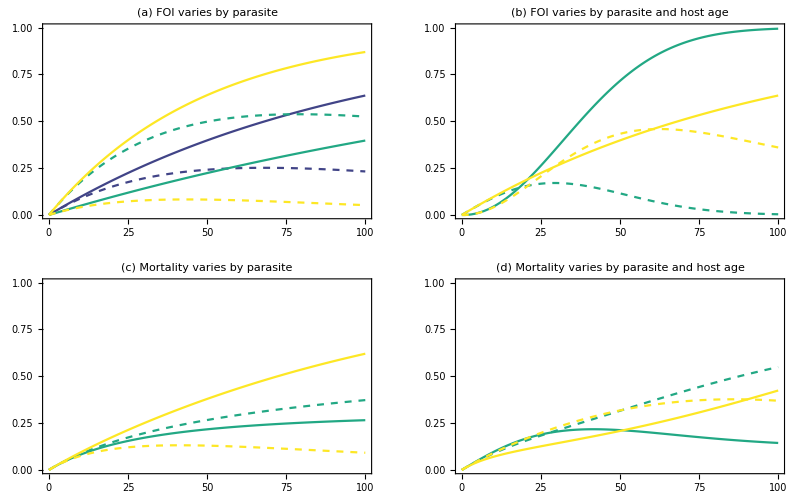
-Graphics-Infection prevalenceHost age

```mathematica
out = model[t,imax,da,0.01, 0.01,0, 0,0.01,0.1,0.01,0.02,7,True,False,True,True];
	pa=MyPlotProp[out,Cols[[2]],"(d) Mortality varies by parasite and host age"];
out = model[t,imax,da,0.01, 0.01,0, 0,0.01,0.1,0.01,0.02,7,True,False,False,True];
	pb=MyPlotProp[out,Cols[[1]]];
p4=Show[pa,pb];

gp=Legended[GraphicsGrid[{{p1,p2},{p3,p4}}],Placed[LineLegend[{Directive[Cols[[3]]],Directive[Cols[[3]],Dashed]},{"Dominant","Subordinate"},LegendLayout->"Row",LegendFunction-> "Frame"],Above]];
final=Labeled[gp,{"Infection prevalence","Host age"},{Left,Bottom,Top},RotateLabel->True,LabelStyle->Directive[FontFamily->"Helvetica",FontSize->14]]
```

```mathematica
Export["FigS_Age-prevalence.pdf",final];
```

#### Snapshots in time

```mathematica
Clear[MyPlotAbund];
MyPlotAbund[out_,Col_,label_:""]:=
ListPlot[
{Table[{i da,u[i][t]},{i,0,imax}],
Table[{i da,d[i][t]},{i,0,imax}],
Table[{i da,s[i][t]},{i,0,imax}]}/.out,
PlotRange->{{0,100},{0,Full}},
PlotStyle->{Directive[Col,Dotted],Directive[Col], Directive[Col,Dashed]},
Axes-> False,
FrameLabel->{"Host age","Abundance"},
Filling->Axis,
PlotLabel->label,
Frame->{True,True,False,False},
Joined->True,
ImageSize->2000];

MyPlotProp2[out_,Col_,label_:""]:=
ListPlot[
{Table[{i da,(u[i][t])/(u[i][t] + d[i][t]+ s[i][t])},{i,0,imax}],Table[{i da,(d[i][t])/(u[i][t] + d[i][t]+ s[i][t])},{i,0,imax}],
Table[{i da,(s[i][t])/(u[i][t] + d[i][t]+ s[i][t])},{i,0,imax}]}/.out,
PlotRange->{{0,100},{0,Full}},
PlotStyle->{Directive[Col,Dotted],Directive[Col], Directive[Col,Dashed]},
Axes-> False,
Filling-> Axis,
PlotLabel->label,
FrameLabel->{"Host age","Proportion"},
Frame->{True,True,False,False},
Joined->True,
ImageSize->2000];
```

```mathematica
times={0,5,10,50,75,200};
imax = 100;
da = 1;
ts=Table[
out=model[t,imax,da,0.01, 0.01,0, 0,0.01,0.01,0.01,7,7,False,False,True,True];
{StringForm["Time = `1`",t],
MyPlotAbund[out,Cols[[3]]],
Quiet@MyPlotProp2[out,Cols[[3]]]},
{t,times}];
finalTS=Legended[GraphicsGrid[ts,ImageSize->Full],
Placed[LineLegend[{Directive[Cols[[3]],Dotted],Directive[Cols[[3]]], Directive[Cols[[3]],Dashed]},{"Uninfected","Dominant","Subordinate"},LegendLayout->"Row",LegendFunction-> "Frame"],Above]];
Export["FigS_TimeSeries.pdf",finalTS];
```